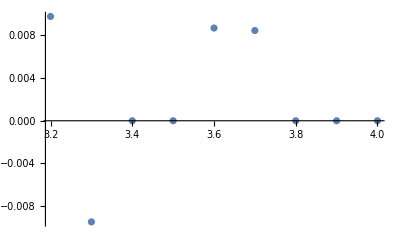

```mathematica
a41={{3.2,75/(3.2×32)},{3.3,78/(3.3×32)},{3.4,82/(3.4×32)},{3.5,86/(3.5×32)}, {3.6,90/(3.6×32)},{3.7,93/(3.7×32)},{3.8,97/(3.8×32)}, {3.9,100/(3.9×32)},{4.0,104/(4×32)}};
a42={{3.2,74/(3.2×32)},{3.3,79/(3.3×32)},{3.4,82/(3.4×32)},{3.5,86/(3.5×32)}, {3.6,89/(3.6×32)},{3.7,92/(3.7×32)},{3.8,97/(3.8×32)}, {3.9,100/(3.9×32)},{4.0,104/(4×32)}};
a4=a41-a42*Table[{0,1},{i,0,8}];
ListPlot[{a4}]
```

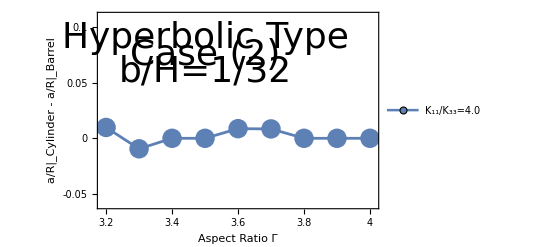

```mathematica
ListPlot[{a4},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{-0.05,0,0.05,0.1},None},{{3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4},None}}, PlotRange->{{3.19,4.01},{-0.06,0.11}},FrameLabel->{{"a/R|_Cylinder - a/R|_Barrel", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],20}}],{Right,Bottom}],Epilog->{Text[Style["Hyperbolic Type",Directive[Black,36]],{3.5,0.09}],Text[Style["Case (2)",Directive[Black,36]],{3.5,0.075}],
Text[Style["b/H=1/32",Directive[Black,36]],{3.5,0.06}]}]
```